```mathematica
Clear["Global`*"]
Needs["Developer`"]
Needs["CCompilerDriver`"]
Needs["Developer`"]
ClearAll[ReadMSHFile,DumpMSHFileTo2DATFiles,ReadMSHFileFrom2DATFiles]
ReadMSHFile[filename_]:=Module[{i,SkipStreamNumbers,ReadStreamNumbers,meshStr,nNodes,nodesTable,nElements,nPoints,nLines,nTriangles,trianglesTable,temp},
SkipStreamNumbers=Skip[#1,Table[Number,{i,Range[#2]}]]&;
ReadStreamNumbers=Read[#1,Table[Number,{i,Range[#2]}]]&;
meshStr=OpenRead[filename];
Find[meshStr,"$Nodes"];
nNodes=Read[meshStr,Number];
nodesTable=ConstantArray[0.0,{nNodes,2}];
For[i=1,i≤nNodes,i++,
Skip[meshStr,Number];
nodesTable⟦i⟧=N@ReadStreamNumbers[meshStr,2];
Skip[meshStr,Number];
];
Find[meshStr,"$Elements"];
nElements=Read[meshStr,Number];
nPoints=0;nLines=0;nTriangles=0;
trianglesTable=ConstantArray[0.0,{nElements,3}];
For[i=1,i≤nElements,i++,
Skip[meshStr,Number];
temp=Read[meshStr,Number];
If[temp==15,nPoints++;SkipStreamNumbers[meshStr,4];];
If[temp==1,nLines++;SkipStreamNumbers[meshStr,5];];
If[temp==2,nTriangles++;SkipStreamNumbers[meshStr,3];trianglesTable⟦nTriangles⟧=N@ReadStreamNumbers[meshStr,3];];
];
trianglesTable=trianglesTable⟦1;;nTriangles⟧;
Close[meshStr];
ToPackedArray/@{nodesTable,Floor@trianglesTable}
]
DumpMSHFileTo2DATFiles[mshfilename_]:=Module[{dir,nodesTable,trianglesTable},
{nodesTable,trianglesTable}=ReadMSHFile[mshfilename];
dir=FileNameJoin[{DirectoryName[mshfilename],FileBaseName[mshfilename]<>".dat"}];
CreateDirectory[dir]//Quiet;
Print["directory created:",dir];
Export[FileNameJoin[{dir,"nodes.dat"}],nodesTable];
Export[FileNameJoin[{dir,"triangles.dat"}],trianglesTable];
Print["exported nodes file: ",FileNameJoin[{dir,"nodes.dat"}]];
Print["exported triangles file: ",FileNameJoin[{dir,"triangles.dat"}]];
]
ReadMSHFileFrom2DATFiles[mshfilename_]:=Module[{dir},
dir=FileNameJoin[{DirectoryName[mshfilename],FileBaseName[mshfilename]<>".dat"}];
Print["imported nodes file: ",FileNameJoin[{dir,"nodes.dat"}]];
Print["imported triangles file: ",FileNameJoin[{dir,"triangles.dat"}]];
ToPackedArray/@{N@Import[FileNameJoin[{dir,"nodes.dat"}]],Import[FileNameJoin[{dir,"triangles.dat"}]]}
]
```

```mathematica
Needs["CCompilerDriver`"]
ClearAll[cflags,dir,incdir,libdir,xlib,src,lib]
cflags="-O3 -Wall -fopenmp -m64";
dir=FileNameJoin[{NotebookDirectory[],"../src/mll"}];
incdir="/opt/intel/mkl/include";
libdir="/opt/intel/mkl/lib/intel64";
xlib="";
(*xlib={"fftw3","mkl_core","mkl_intel_lp64","mkl_sequential","pthread","m"};*)
(*xlib="-lmkl_intel_lp64 -lmkl_core -lmkl_sequential -lpthread -lm";*)
(*xlib={"-lmkl_intel_lp64","-lmkl_core","-lmkl_sequentia;","-lpthread","-lm"};*)
src={"dunavant-rule.cpp","legendre-rule.cpp","arcsinh-rule.cpp","mll.cpp"}//Map[FileNameJoin[{dir,#}]&,#]&;
lib=CreateLibrary[src,"libmll","Libraries"->xlib,"IncludeDirectories"->incdir,"LibraryDirectories"->libdir,"CompileOptions"->cflags];
(*lib=CreateLibrary[src,"libmll","Libraries"->"fftw3","CompileOptions"->cflags];*)
ClearAll[cflags,dir,incdir,libdir,xlib,src]
Print["lib=",lib];

ClearAll[LegendreRule,DunavantRule,ArcSinhRule]
LegendreRule=LibraryFunctionLoad[lib,"LegendreRule_MLL",{Integer,Real,Real},{Real,2,"Shared"}];
DunavantRule=LibraryFunctionLoad[lib,"DunavantRule_MLL",{Integer,{Real,2,"Constant"}},{Real,2,"Shared"}];
ArcSinhRule=LibraryFunctionLoad[lib,"ArcSinhRule_MLL",{{Real,2,"Constant"},{Real,1,"Constant"},{Real,2,"Constant"},{Real,2,"Constant"}},{Real,2,"Shared"}];

ClearAll[VHomoFull,BHomo,BHomoFull,BHomoS,BHomoN,HomoMul]
VHomoFull=LibraryFunctionLoad[lib,"VHomoFull_MLL",{{Real,3,"Constant"},Real,Real,Real,Integer,Integer,Integer,Integer,Integer},{Complex,1,"Shared"}];
BHomo=LibraryFunctionLoad[lib,"BHomo_MLL",{{Real,3,"Constant"},Integer,Integer,Integer,Integer,Integer},{Real,3,"Shared"}];
BHomoFull=LibraryFunctionLoad[lib,"BHomoFull_MLL",{{Real,3,"Constant"},Integer,Integer,Integer,Integer,Integer,Integer},{Real,3,"Shared"}];
BHomoS=LibraryFunctionLoad[lib,"BHomoS_MLL",{Integer,Integer,{Real,1,"Constant"},{Real,2,"Constant"}},{Real,1,"Shared"}];
BHomoN=LibraryFunctionLoad[lib,"BHomoN_MLL",{Integer,Integer,{Real,1,"Constant"},{Real,2,"Constant"}},{Real,1,"Shared"}];
HomoMul=LibraryFunctionLoad[lib,"HomoMul_MLL",{{Complex,1,"Constant"},{Real,1,"Constant"},{Real,3,"Constant"},{Real,1,"Constant"},Real,Real},{Complex,1,"Shared"}];

(*
{{"rule","order","positive"}}~Join~Table[{rule,DunavantRule[rule,{{0,0},{0,1},{1,0}}]//Dimensions//#⟦2⟧&,DunavantRule[rule,{{0,0},{0,1},{1,0}}]//Quiet//Map[Positive,#]&//Flatten//DeleteDuplicates//#⟦1⟧&},{rule,20}]//Quiet//TableForm
ClearAll[pp,p0,nu,nv,qu,qv]
LegendreRule[10,0,1]//Quiet;
DunavantRule[10,{{1,0},{3,2},{0,2}}]//Quiet;
pp={{1,0},{0,2},{3,2}};
p0={3,0};
{nu,nv}={3,2};
qu=LegendreRule[nu,0,1]//Quiet;
qv=LegendreRule[nv,0,1]//Quiet;
ArcSinhRule[pp,p0,qu,qv]//Quiet;
ClearAll[pp,p0,nu,nv,qu,qv]
*)

(*
ClearAll[test,raw]
test=LibraryFunctionLoad[lib,"test",{{Complex,1,"Constant"}},{Complex,2,"Shared"}];
raw=RandomComplex[1+ⅈ,500000];
test[raw]//Quiet//AbsoluteTiming//#⟦1⟧&
ClearAll[raw]
*)

(*
LibraryFunctionUnload[test];
LibraryUnload[lib]
*)
```

lib=/home/qzmfrank/.Mathematica/SystemFiles/LibraryResources/Linux-x86-64/libmll.so

```mathematica
ClearAll[InTriangle,PickTriangle]
InTriangle[v_,ptn_]:=Module[{det,v0,v1,v2,a,b},
det=#1⟦1⟧#2⟦2⟧-#1⟦2⟧#2⟦1⟧&;
v0=ptn⟦1⟧;
v1=ptn⟦2⟧-v0;
v2=ptn⟦3⟧-v0;
a=(det[v,v2]-det[v0,v2])/det[v1,v2];
b=-(det[v,v1]-det[v0,v1])/det[v1,v2];
a>0.0&&b>0.0&&a+b<1.0
]
PickTriangle[v_]:=Module[{n},For[n=1,n≤Ns,n++,If[InTriangle[v,pt⟦n⟧],Break[]]];n]
ClearAll[HalfLineTriangleSegmentC,P0,PT,alpha]
HalfLineTriangleSegmentC=Compile[{{alpha,_Real},{p,_Real,1},{pt,_Real,2}},
Module[{n,d,ds,pts,k,t},
n={Cos[alpha],Sin[alpha]};d=Det[{#-p,n}]&/@pt;ds=Sort[d];
If[ds⟦1⟧ds⟦3⟧≤0.0&&!(Abs[ds⟦1⟧]<1.0*10^-15&&Abs[ds⟦3⟧]<1.0*10^-15),0.0;,Return[0.0];];
k={0,0,0};
k⟦1⟧=Position[d,ds⟦1⟧]⟦1,1⟧;k⟦3⟧=Position[d,ds⟦3⟧]⟦1,1⟧;
k⟦2⟧=Delete[Range[3],{{k⟦1⟧},{k⟦3⟧}}]⟦1⟧;pts=pt⟦k⟦#⟧⟧&/@Range[3];
t=If[ds⟦1⟧*ds⟦2⟧≥0,
{-Det[{pts⟦3⟧-pts⟦1⟧,p-pts⟦1⟧}]/Det[{pts⟦3⟧-pts⟦1⟧,n}],-Det[{pts⟦3⟧-pts⟦2⟧,p-pts⟦2⟧}]/Det[{pts⟦3⟧-pts⟦2⟧,n}]},
{-Det[{pts⟦2⟧-pts⟦1⟧,p-pts⟦1⟧}]/Det[{pts⟦2⟧-pts⟦1⟧,n}],-Det[{pts⟦3⟧-pts⟦1⟧,p-pts⟦1⟧}]/Det[{pts⟦3⟧-pts⟦1⟧,n}]}
];
t=Sort[t];
t⟦1⟧=Max[t⟦1⟧,0.0];
t⟦2⟧=Max[t⟦2⟧,0.0];
t⟦2⟧-t⟦1⟧
]
(*,CompilationTarget:>"C"*)
];
P0={0,-√3/2}//N;PT={{0,0},{1,0},{1/2,√3/2}}//N;alpha=π/3//N;
Plot[HalfLineTriangleSegmentC[alpha,P0,PT],{alpha,0,2π},AxesOrigin->{0,0}];
```

```mathematica
ClearAll[Draw2Trig]
Draw2Trig[n_,np_]:=Show[
ListPlot[pt⟦n⟧,PlotRange->{{0,1},{0,1}},PlotStyle->{Blue,PointSize[Large]},Epilog->{Blue,Line[{pt⟦n,1⟧,pt⟦n,2⟧,pt⟦n,3⟧,pt⟦n,1⟧}],Red,Line[{pt⟦np,1⟧,pt⟦np,2⟧,pt⟦np,3⟧,pt⟦np,1⟧}]}],
ListPlot[pt⟦np⟧,PlotStyle->{Red,PointSize[Large]}]
]
```

```mathematica
ClearAll[PlotFluenceX0]
PlotFluenceX0[X_,y_]:=Module[{data,coord,index,pltdata},
data=Partition[X,2Nd+1][[All,Nd+1]]//Re;
coord=Table[{x,y},{x,0.01,0.99,0.9/Sqrt[Ns]}]//ToPackedArray;
index=PickTriangle/@coord//ToPackedArray;
pltdata={coord[[All,1]],data[[index]]}//Transpose;
(*PackedArrayQ/@{data,coord,index,pltdata}//Print;*)
ListPlot[pltdata,PlotRange->{0,1/(2π)+0.01},AxesLabel->{"x","fluence"}]
]
ClearAll[PlotFluenceX1]
PlotFluenceX1[X_,y_]:=Module[{data,coord,base,index,pltdata},
data=Partition[X,2Nd+1][[All,Nd+1]]//Re;
coord=Table[{x,y},{x,0.01,0.99,0.9/Sqrt[Ns]}]//ToPackedArray;
base=1/(2π)Exp[-μt#[[1]]]&/@coord//ToPackedArray;
index=PickTriangle/@coord//ToPackedArray;
pltdata=data[[index]]+base;
Show[ListPlot[{coord[[All,1]],pltdata}//Transpose,PlotRange->{0,1/(2π)+0.01},AxesLabel->{"x","fluence"}],
Plot[Exp[-μt x]/(2π),{x,0,1},PlotStyle->{Thick,Red,Dashed},PlotRange->{0,1/(2π)+0.01}]]
]
```

### Input

```mathematica
Needs["Developer`"]

ClearAll[filename,μa,μs,μt,g,phis,Nd,padding]
(*filename=FileNameJoin[{NotebookDirectory[],"../msh","t4.msh"}];*)
filename=FileNameJoin[{NotebookDirectory[],"../msh","square162.msh"}];
DumpMSHFileTo2DATFiles[filename];
(*
mus[{x_,y_}]:=2x^2+y+Exp[-0.1x-0.2y]
mua[{x_,y_}]:=x+3y^2-Exp[-0.5x+y^2]
*)
(*
mus[{x_,y_}]:=2Log[2]
mua[{x_,y_}]:=Log[2]
mut[{x_,y_}]:=mua[{x,y}]+mus[{x,y}]
*)
{μa,μs}={Log[3.0],2Log[2.0]};
μt=μa+μs;
g=0.6;
phis=0;
Nd=10;
padding=1;

ClearAll[iG,iL,ToCmplxPckdArry]
iG[{n_,m_},{Ns_,Nd_}]:=(n-1)*(2Nd+1)+m+Nd+1
iL[ng_,{Ns_,Nd_}]:={IntegerPart[(ng-1)/(2Nd+1)+1],Mod[ng-Nd-1,(2Nd+1),-Nd]}
ToCmplxPckdArry=ToPackedArray[N[Re[#]]]+ⅈ ToPackedArray[N[Im[#]]]&;

ClearAll[TriPtPreCalc,CntrPreCalc,r2rRPreCalc,SignedAreaPreCalc]
TriPtPreCalc[p_,t_]:=p⟦#⟧&/@t//ToPackedArray
CntrPreCalc[pt_]:=(Total/@pt)/3.0//ToPackedArray
r2rRPreCalc[cntr_]:=Outer[If[#1<#2,Norm[Subtract@@cntr⟦{#1,#2}⟧],0.0]&,Range[Length[cntr]],Range[Length[cntr]]]//ToPackedArray//#+#ᵀ&
SignedAreaPreCalc[pt_]:=pt//Map[{#⟦1⟧-#⟦2⟧,#⟦1⟧-#⟦3⟧}&,#]&//Map[#⟦1,1⟧#⟦2,2⟧-#⟦1,2⟧#⟦2,1⟧&,#]&//ToPackedArray//Times[#,0.5]&;

ClearAll[Np,p,t,Nm,Ns,Ng,gTbl,iGTbl,iLTbl,pt,cntr,r2rR,area,Tpt,Tcntr,Tr2rR,Tarea]
{p,t}=ReadMSHFileFrom2DATFiles[filename];

(*
(*symmetrize the geometry w.r.p.t. y=0*)
Np=Length[p];
t=t//Join[#,Map[#+ConstantArray[Np,3]&,t]]&;
p=Join[p,{#⟦1⟧,-#⟦2⟧}&/@p];
Np=Length[p];
(*end of symmetrization*)
*)

(*
(*symmetrize the geometry w.r.p.t. x=0*)
Np=Length[p];
t=t//Join[#,Map[#+ConstantArray[Np,3]&,t]]&;
p=Join[p,{-#⟦1⟧,#⟦2⟧}&/@p];
Np=Length[p];
(*end of symmetrization*)
*)

Np=Length[p];Ns=Length[t];Nm=2Nd+1;
Module[{n=Mod[Nm,padding]},If[n≠0,Nm=Nm+padding-n;Nd=Floor[(Nm-1)/2];];];
Ng=Ns(2Nd+1);
Print["{p,t}=",PackedArrayQ/@{p,t}];
Print["{Ns,Nd,Nm,Ng}=",{Ns,Nd,Nm,Ng}];
gTbl=g^Abs[#]&/@Range[-Nd,Nd]//ToPackedArray;
iGTbl=Table[iG[{n,m},{Ns,Nd}],{n,Ns},{m,-Nd,Nd}]//ToPackedArray;
iLTbl=iL[#,{Ns,Nd}]&/@Range[Ng]//ToPackedArray;
Print["{gTbl,iGTbl,iLTbl}=",PackedArrayQ/@{gTbl,iGTbl,iLTbl}];
Tpt=(pt=TriPtPreCalc[p,t];)//AbsoluteTiming//#⟦1⟧&;
Tcntr=(cntr=CntrPreCalc[pt];)//AbsoluteTiming//#⟦1⟧&;
Tr2rR=(r2rR=r2rRPreCalc[cntr];)//AbsoluteTiming//#⟦1⟧&;
Tarea=(area=SignedAreaPreCalc[pt];)//AbsoluteTiming//#⟦1⟧&;
Print["{Tpt,Tcntr,Tr2rR,TsignedArea,Tarea,TRc}=",{Tpt,Tcntr,Tr2rR,Tarea}//{Total[#],#}&];
Print["{pt,cntr,r2rR,signedArea,area,Rc}=",PackedArrayQ/@{pt,cntr,r2rR,area}];
ClearAll[A,B]
A=2π*area;
(*
SetDirectory[FileNameJoin[{"HOME"/.GetEnvironment["HOME"],"tmp"}]];
<<"B.mx";
ResetDirectory[];
*)
ClearAll[RULE1,RULE2,NU,NV]
{RULE1,RULE2,NU,NV}={5,20,2Nd+15,3};
(*BHomo[pt,Nd,Nm,RULE,NU,NV]//Quiet;*)
B=BHomoFull[pt,Nd,Nm,RULE1,RULE2,NU,NV]//Quiet//ToPackedArray;
SetDirectory[FileNameJoin[{"HOME"/.GetEnvironment["HOME"],"tmp"}]];
DumpSave["B.mx",B];
ResetDirectory[];
ClearAll[RULE1,RULE2,NU,NV]

ClearAll[n,np,rc,q0,q1,rule,Nu,Nv,qu,qv]
Print["{A,B}=",PackedArrayQ/@{A,B}];
```

directory created:/home/qzmfrank/codes/rte2dvis/notebook/../msh/square162.dat

exported nodes file: /home/qzmfrank/codes/rte2dvis/notebook/../msh/square162.dat/nodes.dat

exported triangles file: /home/qzmfrank/codes/rte2dvis/notebook/../msh/square162.dat/triangles.dat

imported nodes file: /home/qzmfrank/codes/rte2dvis/notebook/../msh/square162.dat/nodes.dat

imported triangles file: /home/qzmfrank/codes/rte2dvis/notebook/../msh/square162.dat/triangles.dat

{p,t}={True,True}

{Ns,Nd,Nm,Ng}={162,10,21,3402}

{gTbl,iGTbl,iLTbl}={True,True,True}

{Tpt,Tcntr,Tr2rR,TsignedArea,Tarea,TRc}={0.05992,{0.00013,0.00016,0.05918,0.00045}}

{pt,cntr,r2rR,signedArea,area,Rc}={True,True,True,True}

{A,B}={True,True}

### V0

Max Relative err=3.76879×10^-11

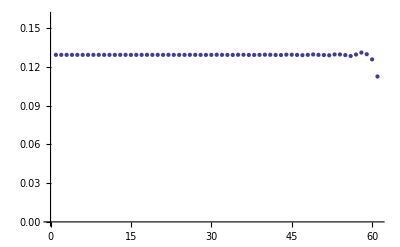

```mathematica
ClearAll[μt,μs,V0]
μt=Log[4.0];
μs=0;
V0=Table[area⟦n⟧Exp[-ⅈ m phis],{n,Ns},{m,-Nd,Nd}]//Flatten//ToPackedArray;
V0//PackedArrayQ;
ClearAll[X0]
X0=LinearSolve[HomoMul[#,A,B,gTbl,μt,μs]&,V0,Method->{"Krylov",Tolerance->10^-20,Method->"GMRES","Preconditioner"->None,MaxIterations->20,"ResidualNormFunction"->Norm}]//Quiet;
Print["Max Relative err=",Abs[(HomoMul[X0,A,B,gTbl,μt,μs]-V0)/V0]//Quiet//Flatten//Max];
ClearAll[data]
data=Re/@(Partition[X0,2Nd+1]⟦1,Nd+1;;2Nd+1⟧)//ToPackedArray;
ListPlot[data,PlotRange->{0,1/(2π)}]//Print;
```

```mathematica
X1=X0;
```

```mathematica
X2=X0;
```

```mathematica
X3=X0;
```

```mathematica
X4=X0;
```

```mathematica
X5=X0;
```

```mathematica
X6=X0;
```

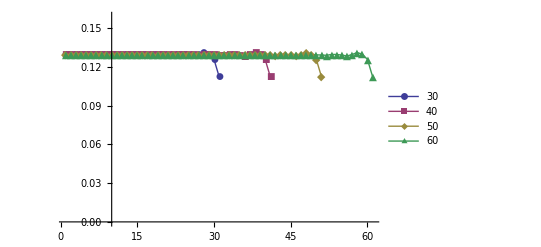

```mathematica
ClearAll[n,raw,nd,data]
n=1;
raw={X1,X2,X3,X4,X5,X6};
nd={10,20,30,40,50,60};
data=Table[Re/@(Partition[raw⟦i⟧,2nd⟦i⟧+1]⟦n,nd⟦i⟧+01;;2nd⟦i⟧+1⟧),{i,6}];
range=Range[3,6];
ListLinePlot[data⟦range⟧,PlotRange->{{1,61},{0,1/(2π)}},PlotMarkers->Automatic,PlotLegends->nd⟦range⟧]
```

### V1 - First Order Extraction

```mathematica
ClearAll[RULE1,RULE2,NU,NV,V1]
{RULE1,RULE2,NU,NV}={5,19,2 Nd+15,3};
V1=VHomoFull[pt,g,phis,μs,Nd,RULE1,RULE2,NU,NV]//Quiet;
ClearAll[X]
X=LinearSolve[HomoMul[#,A,B,gTbl,μt,μs]&,V1,Method->{"Krylov",Tolerance->10^-20,Method->Automatic,"Preconditioner"->Automatic,MaxIterations->30,"ResidualNormFunction"->Automatic}]//Quiet;
Print["Z.X1-V1: max relative err=",Abs[(HomoMul[X,A,B,gTbl,μt,μs]-V1)/V1]//Quiet//Flatten//Max];
```

Z.X1-V1: max relative err=2.27668×10^-14

```mathematica
X1=X;
```

```mathematica
X2=X;
```

```mathematica
X3=X;
```

```mathematica
X4=X;
```

```mathematica
X5=X;
```

```mathematica
X6=X;
```

```mathematica
X7=X;
```

```mathematica
X8=X;
```

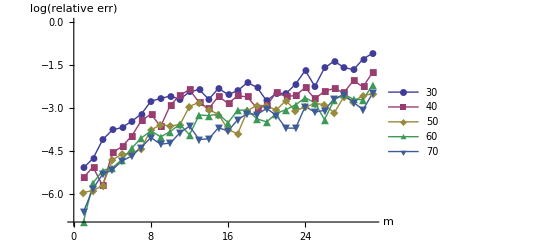

```mathematica
ClearAll[n,raw,nd,data]
n=1;
raw={X1,X2,X3,X4,X5,X6,X7,X8};
nd=Range[10,80,10];
range=Range[3,8];
data=Table[Partition[raw⟦i⟧,2nd⟦i⟧+1]⟦n,nd⟦i⟧+1;;nd⟦i⟧+1+30⟧,{i,range}];
Table[Log[((data⟦i⟧-data⟦-1⟧)/data⟦-1⟧//Abs)]/Log[10],{i,Length[range]-1}]//ListLinePlot[#,PlotRange->Automatic,PlotMarkers->Automatic,PlotLegends->nd⟦range⟧,AxesLabel->{"m","log_10(relative err)"}]&
```